```mathematica
?cols
```

Global`cols

cols={RGBColor[0,0,t],RGBColor[0,t,0],RGBColor[t,0,0],RGBColor[0,1,t],RGBColor[0,t,1],RGBColor[1,0,t],RGBColor[1,t,0],RGBColor[t,0,1],RGBColor[t,1,0],RGBColor[1,1,t],RGBColor[1,t,1],RGBColor[t,1,1]}

```mathematica
colx=RGBColor@@@Tuples[{0,1,t,1-t},3]
```

{RGBColor[0, 0, 0],RGBColor[0, 0, 1],RGBColor[0,0,t],RGBColor[0,0,1-t],RGBColor[0, 1, 0],RGBColor[0, 1, 1],RGBColor[0,1,t],RGBColor[0,1,1-t],RGBColor[0,t,0],RGBColor[0,t,1],RGBColor[0,t,t],RGBColor[0,t,1-t],RGBColor[0,1-t,0],RGBColor[0,1-t,1],RGBColor[0,1-t,t],RGBColor[0,1-t,1-t],RGBColor[1, 0, 0],RGBColor[1, 0, 1],RGBColor[1,0,t],RGBColor[1,0,1-t],RGBColor[1, 1, 0],RGBColor[1, 1, 1],RGBColor[1,1,t],RGBColor[1,1,1-t],RGBColor[1,t,0],RGBColor[1,t,1],RGBColor[1,t,t],RGBColor[1,t,1-t],RGBColor[1,1-t,0],RGBColor[1,1-t,1],RGBColor[1,1-t,t],RGBColor[1,1-t,1-t],RGBColor[t,0,0],RGBColor[t,0,1],RGBColor[t,0,t],RGBColor[t,0,1-t],RGBColor[t,1,0],RGBColor[t,1,1],RGBColor[t,1,t],RGBColor[t,1,1-t],RGBColor[t,t,0],RGBColor[t,t,1],RGBColor[t,t,t],RGBColor[t,t,1-t],RGBColor[t,1-t,0],RGBColor[t,1-t,1],RGBColor[t,1-t,t],RGBColor[t,1-t,1-t],RGBColor[1-t,0,0],RGBColor[1-t,0,1],RGBColor[1-t,0,t],RGBColor[1-t,0,1-t],RGBColor[1-t,1,0],RGBColor[1-t,1,1],RGBColor[1-t,1,t],RGBColor[1-t,1,1-t],RGBColor[1-t,t,0],RGBColor[1-t,t,1],RGBColor[1-t,t,t],RGBColor[1-t,t,1-t],RGBColor[1-t,1-t,0],RGBColor[1-t,1-t,1],RGBColor[1-t,1-t,t],RGBColor[1-t,1-t,1-t]}

```mathematica
colx2=Select[colx,Not[((#/.(t->1/2))===RGBColor[1/2,1/2,1/2])]&&MemberQ[#,t]&];
colx3=DeleteDuplicates[colx2,#1===(#2/.{t->1-t,1-t->t})&]
```

{RGBColor[0,0,t],RGBColor[0,1,t],RGBColor[0,t,0],RGBColor[0,t,1],RGBColor[0,t,t],RGBColor[0,t,1-t],RGBColor[1,0,t],RGBColor[1,1,t],RGBColor[1,t,0],RGBColor[1,t,1],RGBColor[1,t,t],RGBColor[1,t,1-t],RGBColor[t,0,0],RGBColor[t,0,1],RGBColor[t,0,t],RGBColor[t,0,1-t],RGBColor[t,1,0],RGBColor[t,1,1],RGBColor[t,1,t],RGBColor[t,1,1-t],RGBColor[t,t,0],RGBColor[t,t,1],RGBColor[t,1-t,0],RGBColor[t,1-t,1]}

```mathematica
colx4=Select[colx3,Not[(#[[1]]===#[[2]])||(#[[2]]===#[[3]])||(#[[1]]===#[[3]])]&]
```

{RGBColor[0,1,t],RGBColor[0,t,1],RGBColor[0,t,1-t],RGBColor[1,0,t],RGBColor[1,t,0],RGBColor[1,t,1-t],RGBColor[t,0,1],RGBColor[t,0,1-t],RGBColor[t,1,0],RGBColor[t,1,1-t],RGBColor[t,1-t,0],RGBColor[t,1-t,1]}

```mathematica
colx5=Select[colx3,!MemberQ[{RGBColor[1,t,t],RGBColor[0,t,t]},Sort[#]]&]
```

{RGBColor[0,0,t],RGBColor[0,1,t],RGBColor[0,t,0],RGBColor[0,t,1],RGBColor[0,t,1-t],RGBColor[1,0,t],RGBColor[1,1,t],RGBColor[1,t,0],RGBColor[1,t,1],RGBColor[1,t,1-t],RGBColor[t,0,0],RGBColor[t,0,1],RGBColor[t,0,1-t],RGBColor[t,1,0],RGBColor[t,1,1],RGBColor[t,1,1-t],RGBColor[t,1-t,0],RGBColor[t,1-t,1]}

```mathematica
Show[DensityPlot[maxCc3[l,h],{h,0,2},{l,0,1},ColorFunction->GrayLevel,AspectRatio->Automatic,PlotPoints->100],ParametricPlot[Evaluate[{Mod[hue@#+.001,1],luma@#}&@cc[#,LCHColor]],{t,0,1},PlotRange->All,ColorFunction->Function[{h,l,t},#]]&/@colx5,ParametricPlot[Evaluate[{1+Mod[hue@#+.001,1],luma@#}&@cc[#,LCHColor]],{t,0,1},PlotRange->All,ColorFunction->Function[{h,l,t},#]]&/@colx5,Graphics[{RGBColor@@#,EdgeForm[Black],Disk[{hue@#,luma@#}&@cc[RGBColor@@#,LCHColor],.01]}]&/@Tuples[{0,1},3],
Graphics[{RGBColor@@#,EdgeForm[Black],Disk[{1+hue@#,luma@#}&@cc[RGBColor@@#,LCHColor],.01]}]&/@Tuples[{0,1},3]]
```

-Graphics-

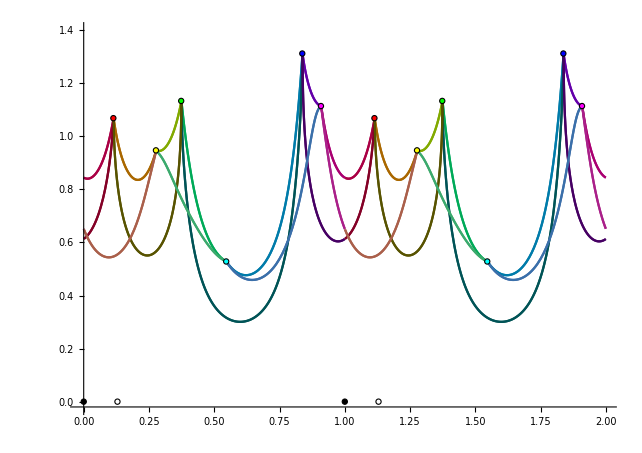

```mathematica
Show[ParametricPlot[Evaluate[{Mod[.001+hue@#,1],chroma@#}&@cc[#,LCHColor]],{t,0,1},PlotRange->{All,{-.02,1.4}},AxesOrigin->{0,-.02},ColorFunction->Function[{h,l,t},Darker@#]]&/@colx4,ParametricPlot[Evaluate[{1+Mod[.001+hue@#,1],chroma@#}&@cc[#,LCHColor]],{t,0,1},PlotRange->All,ColorFunction->Function[{h,l,t},Darker@#]]&/@colx4,Graphics[{RGBColor@@#,EdgeForm[Black],Disk[{Mod[.0001+hue@#,1],chroma@#}&@cc[RGBColor@@#,LCHColor],.01]}]&/@Tuples[{0,1},3],Graphics[{RGBColor@@#,EdgeForm[Black],Disk[{1+Mod[.0001+hue@#,1],chroma@#}&@cc[RGBColor@@#,LCHColor],.01]}]&/@Tuples[{0,1},3]]
```

```mathematica
?AxesOrigin
```

AxesOrigin is an option for graphics functions that specifies where any axes drawn should cross.

```mathematica
step=1/63.
ctab=Flatten[Table[RGBColor[r,g,b],{r,0,1,step},{g,0,1,step},{b,0,1,step}]];
```

0.015873

```mathematica
Length[ctab]
```

262144

```mathematica
ListPlot[lch[cc[#,LCHColor]][[{3,1}]]&/@ctab]
```

-Graphics-

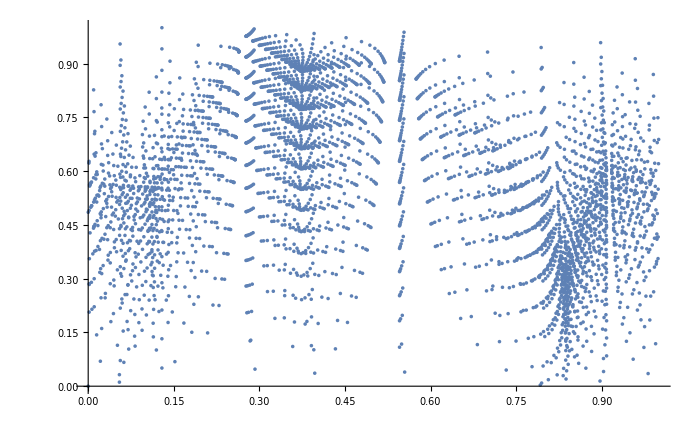

```mathematica
ListPlot[lch[cc[#,LCHColor]][[{3,1}]]&/@ctab]
```

```mathematica
?ListPlot3D
```

RowBox[{"ListPlot", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] plots points RowBox[{RowBox[{"{", RowBox[{"1", ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{"2", ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}]. 
RowBox[{"ListPlot", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] plots a list of points with specified StyleBox["x", "TI"] and StyleBox["y", "TI"] coordinates. 
RowBox[{"ListPlot", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["data", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["data", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] plots data from all the SubscriptBox[StyleBox["data", "TI"], StyleBox["i", "TI"]].
RowBox[{"ListPlot", "[", RowBox[{"{", RowBox[{StyleBox["…", "TR"], ",", RowBox[{StyleBox["w", "TI"], "[", RowBox[{SubscriptBox[StyleBox["data", "TI"], StyleBox["i", "TI"]], ",", StyleBox["…", "TR"]}], "]"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] plots SubscriptBox[StyleBox["data", "TI"], StyleBox["i", "TI"]] with features defined by the symbolic wrapper StyleBox["w", "TI"].